## Black Holes, Worksheet II for Thursday, Oct. 10

## Relativistic Race-Walking (Taylor and Wheeler, Problem 6-6)

## Relativistic Race-Walking

I’m going to assume that you understand the description of what constitutes legal relativistic race-walking. Also, I am going to assume that you understand why the FrontDown and BackUp events must be light-like separated. For short, we’ll call the six events we are going to plot BU -1, FD 0, BU 0, FD 1, BU 1, and FD2, and I’ll have Mathematica do the work of accurately plotting them.

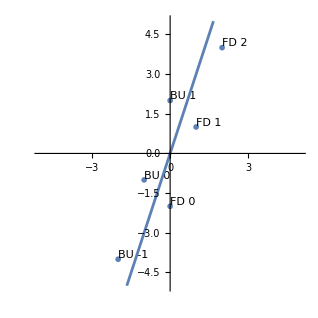

```mathematica
raceWalkerEvents={
Labeled[{-2,-4},"BU -1"],
Labeled[{0,-2},"FD 0"],
Labeled[{-1,-1},"BU 0"],
Labeled[{1,1},"FD 1"],
Labeled[{0,2},"BU 1"], 
Labeled[{2,4},"FD 2"]
};
raceWalkerEventPlot = ListPlot[raceWalkerEvents, PlotRange->{{-5,5},{-5,5}}, AspectRatio->1];
raceWalkerTorsoPlot = Plot[3x,{x, -2, 2}, PlotRange->{{-5,5},{-5,5}}, AspectRatio->1];
Show[raceWalkerEventPlot, raceWalkerTorsoPlot]
```

## 1. Checking Legality and Speed of the Race-Walker

(a) In the plot on the previous page, using three straight, solid lines, connect BU -1 to FD 0, BU 0 to FD 1, and BU 1 to FD 2. Are these the almost-the-speed-of-light, back-up-front-down placements as required by the description in Problem 6-6?

(b) Also on the plot, with two straight but squiggly lines like the squiggly lines that Taylor and Wheeler use on p. 161, mark the separations that connect FD 0 to BU 0, and FD 1 to BU 1. Are these the light-like separations that are required to signal the back foot that it is legal to lift up?

(c) The diagonal line represents the motion of the torso. By measuring off the line on the plot, what speed does the torso have?


(d) Finally, with a straight line, connect FD0 to BU 1. Does this represent a foot at rest?

## 2. Lorentz Transformation

In Problem 1 you checked the legality of the race-walker. Imagine that what was drawn above was actually a super-race-walker as viewed in the frame of an ordinary and legal race-walker. So the super-race-walker has torso speed v=1/3 with respect to the race-walker, who in turn has speed v_rel=1/3 with respect to the Earth.

(a) Using the velocity addition formula, what is the speed of the super-race-walker with respect to the Earth?

(b) It’s a bunch of work to use the Lorentz transformation to transform each event in the plot in Problem 1 to an Earth-frame plot, but we need to do it for all six events to start to see what is going on. I’ll have Mathematica do two-thirds of the work for you.

```mathematica
vRel=1/3; gamma=1/Sqrt[1-vRel^2];
```

To two decimal places, v_rel=0.67, and γ=1.61. Use Equation L-10a on p. 102 to transform the FD 1 coordinates t'=1, x'=1 to t and x coordinates and then add FD 1 to the plot in Problem 3. For your convenience, here is Equation L-10a:

(c) Again use equation L-10a to transform the BU 1 coordinates t'=2, x'=0 to t and x coordinates and then add BU 1 to the plot in Problem 3.

## 3. Checking Legality and Speed of the Super-Race-Walker

As promised, I let Mathematica do two thirds of the work by transforming four of the six points.

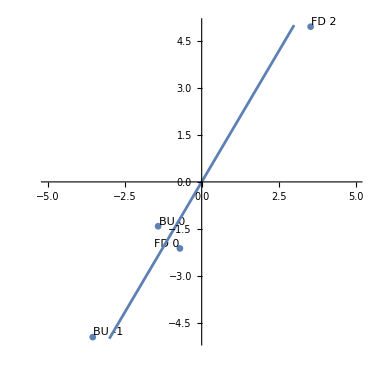

```mathematica
lorentzTransformation[{x_,t_}]:={vRel*gamma*t+gamma*x,vRel*gamma*x+gamma*t};
superRaceWalkerEvents={
Labeled[lorentzTransformation[{-2,-4}],"BU -1"],
Labeled[lorentzTransformation[{0,-2}],"FD 0"],
Labeled[lorentzTransformation[{-1,-1}],"BU 0"],
Labeled[lorentzTransformation[{2,4}],"FD 2"]
};
superRaceWalkerEventPlot = ListPlot[superRaceWalkerEvents, PlotRange->{{-5,5},{-5,5}}, AspectRatio->1];
superRaceWalkerTorsoPlot = Plot[5x/3,{x, -4, 4}, PlotRange->{{-5,5},{-5,5}}, AspectRatio->1];
Show[superRaceWalkerEventPlot, superRaceWalkerTorsoPlot]
```

(a) In the plot on the previous page, using three straight, solid lines, connect BU -1 to FD 0, BU 0 to FD 1, and BU 1 to FD 2. Are these legal almost-the-speed-of-light, back-up-front-down placements?


(b) Also on the plot, with two straight but squiggly lines, mark the separations that connect FD 0 to BU 0, and FD 1 to BU 1. Are these the light-like separations that are required to signal the back foot that it is legal to lift up?


(c) The diagonal line represents the motion of the torso. By measuring off the line on the plot, what speed does the torso have? Does this agree with 2(a)? HINT: If you go up the vertical axis to t=5 and measure across, you’ll find a tidy ratio.


(d) Finally, with a straight line, connect FD 0 to BU 1. Does this represent a foot at rest with respect to the Earth?



(e) Was Harvard Prof. Paul Horowitz right? Do you feel better now about getting things wrong if Prof. Horowitz sometimes gets them wrong too?